## MAT 331: Project 2

## Project description

In this project we will use Mathematica to solve several problems involving differential equations.

## Problem 1

The fish and game department in a certain state is planning to issue hunting permits to control the deer population (one deer per permit). It is known that if the deer population falls below a certain level m, the deer will become extinct. It is also known that if the deer population rises above the carrying capacity M, the population will decrease back to M through disease and malnutrition. Consider the following model for the growth rate of the deer population P as a function of time t:

#### dP/dt=r P(M-P)(P-m)

where P is the deer population and r=0.00003 is a constant of proportionality. The values of the other parameters are M=100 and m=55.

dP/dt=0.00003 P(100-P)(P-55)

Plot the vector field of the differential equation using VectorPlot[..]. Then plot the vector field using StreamPlot[..]; identify the constant solutions and color them in red using StreamPlot[..]. Try a window size of 180x150 (in the txP plane). What happens to the solutions as time t increases, t→∞? Color a couple of trajectories to illustrate the possible behaviors, then explain the plot.

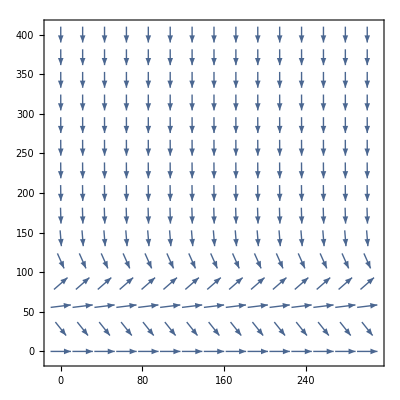

```mathematica
VectorPlot[{1,0.00003*P*(100-P)*(P-55)},{t,0,300},{P,0,400},VectorScale->{Tiny,Small,None}]
```

when p =55 and 100 will have constant solution

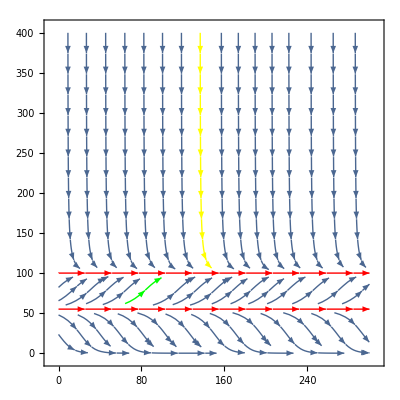

```mathematica
StreamPlot[{1,0.00003*P*(100-P)*(P-55)},{t,0,300},{P,0,400},VectorScale->{Tiny,Small,None},StreamPoints->{{{{0,55},Red},{{0,100},Red} ,{{89,85},Green},{{140,130},Yellow},Automatic}}]
```

I think as time t increases, t→∞, the solution will still around 100.  If deer population rises above 100, the population will decrease back to100. If deer population less than 100 and greater than 55, the population will rises to 100. If the  deer population falls below55, the deer will become extinct.

Solve the system of differential equations for the initial condition P(20)=110. If DSolve[...] does not work, then a numeric approximation may be the next best thing to hope for, so use Mathematica to find a numerical approximation of the true solution, then plot it.

```mathematica
s=DSolve[P'[t]==0.00003*P[t]*(100-P[t])*(P[t]-55),P[t],t]//FullSimplify
```

{{P[t]→InverseFunction[((-2506828579552884149515379015681+21 √169063187920267987306207564337800062803718623205650116752521) Log[1416262354468154771299814854461+√169063187920267987306207564337800062803718623205650116752521-18274352960879419754761158656 #1]+5013657159105768299030758031362 Log[#1]-(2506828579552884149515379015681+21 √169063187920267987306207564337800062803718623205650116752521) Log[-1416262354468154771299814854461+√169063187920267987306207564337800062803718623205650116752521+18274352960879419754761158656 #1])/970213084564975525651239717563107146582720512000&][-8.52651×10^-19 t+C[1]]}}

```mathematica
P[t]/.s
```

{InverseFunction[((-2506828579552884149515379015681+21 √169063187920267987306207564337800062803718623205650116752521) Log[1416262354468154771299814854461+√169063187920267987306207564337800062803718623205650116752521-18274352960879419754761158656 #1]+5013657159105768299030758031362 Log[#1]-(2506828579552884149515379015681+21 √169063187920267987306207564337800062803718623205650116752521) Log[-1416262354468154771299814854461+√169063187920267987306207564337800062803718623205650116752521+18274352960879419754761158656 #1])/970213084564975525651239717563107146582720512000&][-8.52651×10^-19 t+C[1]]}

```mathematica
s1=NDSolve[{P'[t]==0.00003*P[t]*(100-P[t])*(P[t]-55),P[0]==110},P[t],{t,0,200}]
```

{{P[t]→InterpolatingFunction[{{0., 200.}}, <>][t]}}

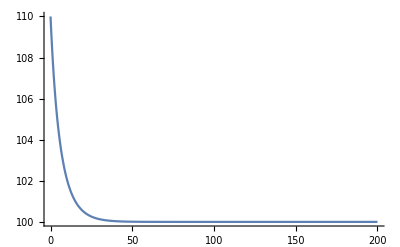

```mathematica
Plot[P[t]/.s1,{t,0,200},PlotRange->All]
```

If the initial deer population is 140, about how many hunting permits should be issued so that the deer population does not become extinct?

```mathematica
s2=NDSolve[{P'[t]==0.00003*P[t]*(100-P[t])*(P[t]-55),P[0]==140},P[t],{t,0,200}]
```

{{P[t]→InterpolatingFunction[{{0., 200.}}, <>][t]}}

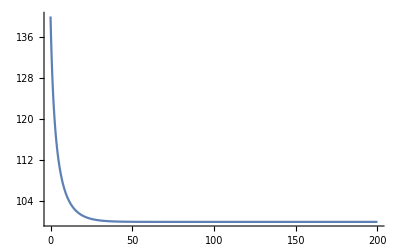

```mathematica
Plot[P[t]/.s2,{t,0,200},PlotRange->All]
```

as t increasing, the deer population will be around 100, because m=55, so 100-55=45, so less than 45 hunting permits can be issued.

Write a small interactive model using Manipulate[..] and Locator[..], that initially plots the StreamPlot[..] from part 1, and then on click, colors the solution curve that passes through the point where the user clicked.

```mathematica
splot=StreamPlot[{1,0.00003*P*(100-P)*(P-55)},{t,0,300},{P,0,400}, ImageSize->Large];
Manipulate[Show[splot,
ParametricPlot[
Evaluate[{P[t]}/.DSolve[{P'[t]==0.00003*P[t]*(100-P[t])*(P[t]-55)},{P},{t,0,T}]],{t,0,T},PlotStyle->Red]
 ],
{{T,10},1,100},
{{point,{1,0}},Locator},
SaveDefinitions->True]
```

## Problem 2

Consider the system of differential equations given below, where α  is a real parameter:

#### x’[t] = -x[t] + αy[t] y’[t] = -x[t] - y[t]

Find the eigenvalues and eigenvectors of the coeffient matrix of the given system in terms of the parameter α.

```mathematica
A={{-1,α},{-1,-1}}; 
Eigensystem[A]
```

{{-1-√-α,-1+√-α},{{√-α,1},{-√-α,1}}}

Assume that the value of the parameter α is 4.

x’ = -x + 4y
   y’ =  -x - y

Assume that the system satisfies the initial condition x(0)=1 and y(0)=1. Use DSolve[..] to find the solution of the corresponding initial value problem, then plot the correspoding trajectory in the xy plane.

```mathematica
sol1=DSolve[{x'[t]==-x[t]+4*y[t], y'[t]==-x[t]-y[t],x[0]==1,y[0]==1},{x[t],y[t]},t]
```

{{x[t]→ⅇ^-t (Cos[2 t]+2 Sin[2 t]),y[t]→1/2 ⅇ^-t (2 Cos[2 t]-Sin[2 t])}}

```mathematica
{x1[t_],y1[t_]}= {x[t] ,y[t]}/. Flatten[sol1]
```

{ⅇ^-t (Cos[2 t]+2 Sin[2 t]),1/2 ⅇ^-t (2 Cos[2 t]-Sin[2 t])}

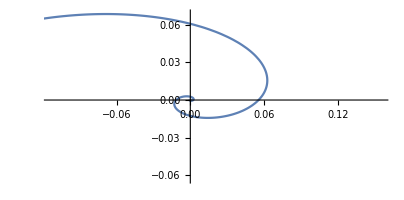

```mathematica
ParametricPlot[{x1[t],y1[t]},{t,0,10}]
```

For your trajectory in part 2.0.1, draw the graphs of x versus t and y versus t on the same graph.

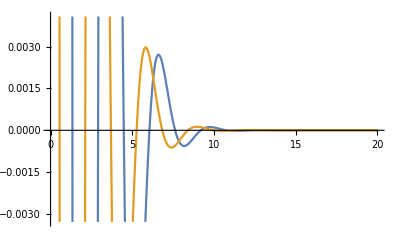

```mathematica
x1[t_]=ⅇ^-t (Cos[2 t]+2 Sin[2 t]);
y1[t_]=1/2 ⅇ^-t (2 Cos[2 t]-Sin[2 t]);
Plot[{x1[t],y1[t]},{t,0,20}]
```

For your trajectory in part 2.0.1, draw the corresponding graph in the three-dimensional txy-space.

In parts 2.0.1 - 2.0.3, it is important that you choose appropriate appropriate ranges for x,y,t and approriate scales for your plot.

```mathematica
sol1=DSolve[{x'[t]==-x[t]+4*y[t], y'[t]==-x[t]-y[t],x[0]==1,y[0]==1},{x[t],y[t]},t]
```

{{x[t]→ⅇ^-t (Cos[2 t]+2 Sin[2 t]),y[t]→1/2 ⅇ^-t (2 Cos[2 t]-Sin[2 t])}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],t}/.sol1],{t,0,5}]
```

-Graphics3D-

Assume that the value of the parameter α is -4.

x’ = -x - 4y
   y’ =  -x - y

Plot the vector field using StreamPlot[...]. On the same plot, plot the eigenvectors (eigenfunctions) from part 1.

```mathematica
Clear[x,y]
```

```mathematica
Manipulate[Row[{Column[{Text["MATRIX"],MatrixForm[m],Text["EIGENVALUES"], N[Eigenvalues[m]]}, Spacings->2], StreamPlot[{{-1,-4},{-1,-1}}.{x,y},{x,-5,5},{y,-5,5},StreamScale->Large,ImageSize->Large]}],{{m,({{-1,-4},{-1,-1}})}}]
```

Describe the long term behavior of the solutions as t→∞.

```mathematica
ClearAll[x,y]
```

```mathematica
sol3=DSolve[{x'[t]==-x[t]-4*y[t], y'[t]==-x[t]-y[t]},{x[t],y[t]},t]
```

{{x[t]→1/2 ⅇ^(-3 t) (1+ⅇ^(4 t)) C[1]-ⅇ^(-3 t) (-1+ⅇ^(4 t)) C[2],y[t]→-1/4 ⅇ^(-3 t) (-1+ⅇ^(4 t)) C[1]+1/2 ⅇ^(-3 t) (1+ⅇ^(4 t)) C[2]}}

```mathematica
{x3[t_],y3[t_]}= {x[t] ,y[t]}/. Flatten[sol3]
```

{1/2 ⅇ^(-3 t) (1+ⅇ^(4 t)) C[1]-ⅇ^(-3 t) (-1+ⅇ^(4 t)) C[2],-1/4 ⅇ^(-3 t) (-1+ⅇ^(4 t)) C[1]+1/2 ⅇ^(-3 t) (1+ⅇ^(4 t)) C[2]}

we don’t know what’s the value of C[1]  and C[2].
If the  C[1]  and C[2] >0 .  as t→∞, x will be approaching to -∞, and y is  approaching to +∞.
If the  C[1]  and C[2]<0 .  as t→∞, y will be approaching to -∞, and x is  approaching to +∞.
If the  C[1]  <0and C[2] >0 .  as t→∞, x will be approaching to +∞, and y is  approaching to +∞.
If the  C[1]  >0and C[2] <0 .  as t→∞, x will be approaching to -∞, and y is  approaching to -∞.

Assume that the system satisfies the initial condition x(0)=1 and y(0)=1. Use DSolve[..] to find the solution of the corresponding initial value problem, then plot the correspoding trajectory in the xy plane.

```mathematica
sol2=DSolve[{x'[t]==-x[t]-4*y[t], y'[t]==-x[t]-y[t],x[0]==1,y[0]==1},{x[t],y[t]},t]
```

{{x[t]→-1/2 ⅇ^(-3 t) (-3+ⅇ^(4 t)),y[t]→1/4 ⅇ^(-3 t) (3+ⅇ^(4 t))}}

```mathematica
{x2[t_],y2[t_]}= {x[t] ,y[t]}/. Flatten[sol2]
```

{-1/2 ⅇ^(-3 t) (-3+ⅇ^(4 t)),1/4 ⅇ^(-3 t) (3+ⅇ^(4 t))}

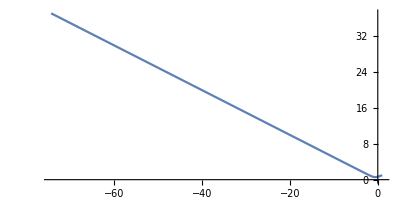

```mathematica
ParametricPlot[{x2[t],y2[t]},{t,0,5}]
```

By using Manipulate[...] and StreamPlot[..], do an interactive model of the vector field of the system, with the parameter α  taking values in the closed interval [- 4, 4].

```mathematica
Manipulate[StreamPlot[{-x+α*y,-x-y},{x,-5,5},{y,-5,5},StreamScale->Automatic],{α,-4,4}]
```

Use the interactive model to find the values of the parameter α where the qualitative nature of the solutions for the system changes. Then try to explain the change in terms of the eigenvalues of the system.

```mathematica
A={{-1,α},{-1,-1}};
```

```mathematica
Eigenvalues[A]
```

{-1-√-α,-1+√-α}

```mathematica
Manipulate[Eigenvalues[{{-1,α},{-1,-1}}],{α,-4,4}]
```

When  α=0, the qualitative nature of the solutions for the system changes.  α>0, the eigenvalues become complex.

## General considerations:

No previous knowledge of differential equations is assumed is this project, except for the theory developed in the lecture notes posted on Blackboard. Please read also the lab notes on Blackboard to find what Mathematica commands are used for solving differential equations. More examples and tutorials about solving differential equations and plotting vector fields can be found in the Mathematica documentation.